```mathematica
ClearAll["Global`*"]
```

```mathematica
SC344C={{1.,1.68},{1.6081819581280792,2.0476190476190474},{2.9050141967706624,1.345238095238095},{3.3008560823754785,1.0982142857142854}};
SuNAM={{2.2905505952380953,1.5119047619047619},{3.300300184729064,0.9047619047619044}};
SCS4050={{0.6064458470169677,1.443452380952381},{1.6115258962780517,1.2113095238095235},{2.9043471195949646,1.113095238095238},{3.903226772030651,0.7232142857142854}};
SCS4050AP={{2.3007021414887796,1.044642857142857},{2.9037997742200328,0.9226190476190472},{3.305089456759716,0.571428571428571},{3.908264059934319,0.47619047619047583}};
SCS4050AP2013={{2.3011981732348112,1.2172619047619047},{3.305688115763547,0.7797619047619047}};
```

```mathematica
(*F[fL_,c_,n_,d_,ϵ_]:=Piecewise[{{1,0<fL<ϵ},{(1-d*fL^n+Log[d*fL^n])/Log[d*fL^n]*(1+c*d*fL^n)+(1-(1-d*ϵ^n+Log[d*ϵ^n])/Log[d*ϵ^n]*(1+c*d*ϵ^n)),ϵ<fL}}]*)
phif[x_,d_,n_]:=d*x^n
f[ϕ_,c_]:=(1-ϕ+Log[ϕ])/Log[ϕ]*(1+c*ϕ)
F[fL_,fL0_,c_,n_,d_]:=f[phif[fL/fL0,d,n],c]
```

```mathematica
Manipulate[{Plot[Min[1,phif[fL/fL0,d,n]],{fL,0,10}],Plot[F[fL,fL0,c,n,d],{fL,0,10},PlotRange->Full],Plot[{f[ϕ,c],f[ϕ+ϵ,c]/f[ϵ,c],1},{ϕ,0,1},PlotLegends->{"Original","Shifted","1"}]},{{c,10},0,100},{{n,1.346},0,1.4},{{d,1.56*10^-6},0,0.00001},{{fL0,0.0004},0,1},{ϵ,0.00000000000001,0.5}]
```

```mathematica
(*344C*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,fL01,data,Ef,xmax]
data=SC344C;
n1= 0.33318;
Ef[fL0_,c_,n_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,n1,d1],d1>0.1&&c1>0.1},{c1,d1}]
(*fL02=fL01/.Soln[[2]]*)
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
c344C=c2; 
d344C=d2; 
Manipulate[Plot[{F[fL,fL0,c,n,d]},{fL,0,10},PlotRange->{0,2.2},Epilog->{PointSize[Medium],Point[{{SC344C[[1,1]],SC344C[[1,2]]},{(SC344C[[2,1]]),SC344C[[2,2]]}, {(SC344C[[3,1]]),SC344C[[3,2]]}, {(SC344C[[4,1]]),SC344C[[4,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n,n1},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{0.156614,{c1→11.8861,d1→0.994899}}

11.8861

0.994899

```mathematica
(*SuNAM*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,fL01,data,Ef,xmax]
data=SuNAM
Ef[fL0_,c_,n_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
n1= 0.33318;
Soln=NMinimize[{Ef[fL01,c1,n1,d1],d1>0.1&&c1>0.1},{c1,d1}]
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
cSuNAM=c2; 
dSuNAM=d2; 
Manipulate[Plot[{F[fL,fL0,c,n,d]},{fL,0,7},PlotRange->{0,10},Epilog->{PointSize[Medium],Point[{{SuNAM[[1,1]],SuNAM[[1,2]]},{(SuNAM[[2,1]]),SuNAM[[2,2]]}}]},ImageSize->Large],{{c,c2},0,100},{{n,n1},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{{2.29055,1.5119},{3.3003,0.904762}}

{3.90389×10^-16,{c1→15.5512,d1→1.12959}}

15.5512

1.12959

```mathematica
(*SCS4050*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,fL01,data,Ef,xmax]
data=SCS4050;
n1= 0.33318;
Ef[fL0_,c_,n_,d_]:=Sum[(data[[k,2]]-F[data[[k,1]],fL0,c,n,d])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];
fL01=7;
Soln=NMinimize[{Ef[fL01,c1,n1,d1],d1>0.1&&c1>0.1},{c1,d1}]
(*fL02=fL01/.Soln[[2]]*)
c2=c1/.Soln[[2]]
d2=d1/.Soln[[2]]
cSCS4050=c2; 
dSCS4050=d2; 
Manipulate[Plot[{F[fL,fL0,c,n,d]},{fL,0,10},PlotRange->{0,2.2},Epilog->{PointSize[Medium],Point[{{SCS4050[[1,1]],SCS4050[[1,2]]},{(SCS4050[[2,1]]),SCS4050[[2,2]]}, {(SCS4050[[3,1]]),SCS4050[[3,2]]}, {(SCS4050[[4,1]]),SCS4050[[4,2]]}}]},ImageSize->Large],{{c,c2},0,20},{{n,n1},0,2},{{d,d2},0,10},{{fL0,fL01},0,20}]
```

{0.0206972,{c1→7.96071,d1→0.962967}}

7.96071

0.962967

```mathematica
(*phif[x_,d_,n_]:=d*x^n
f[ϕ_,c_]:=(1-ϕ+Log[ϕ])/Log[ϕ]*(1+c*ϕ)
F[fL_,fL0_,c_,n_,d_]:=f[phif[fL/fL0,d,n],c]*)
```

```mathematica
(*SCS4050AP*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,fL01,data,Ef,Ef1,xmax]
data=SCS4050AP
n1= 0.33318;
c1=7.960713761601107;
d1=0.9629666482208151;
fL01=7;
Ef1[fL0_,c_,n_,d_, ϵ_]:=Sum[(data[[k,2]]-f[phif[data[[k,1]]/fL0,d,n]+ϵ,c]/f[ϵ,c])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];

Soln=NMinimize[{Ef1[fL01,c1,n1,d1, ϵ1],ϵ1>0},{ϵ1}]
(*fL02=fL01/.Soln[[2]]*)
ϵ2=ϵ1/.Soln[[2]]
ϵSCS4050AP=ϵ2; 
(*d2=d1/.Soln[[2]]*)
Manipulate[Plot[{f[phif[fL/fL0,d,n]+ϵ,c]/f[ϵ,c]},{fL,0,10},PlotRange->{0,2.2},Epilog->{PointSize[Medium],Point[{{SCS4050AP[[1,1]],SCS4050AP[[1,2]]},{(SCS4050AP[[2,1]]),SCS4050AP[[2,2]]}, {(SCS4050AP[[3,1]]),SCS4050AP[[3,2]]}, {(SCS4050AP[[4,1]]),SCS4050AP[[4,2]]}}]},ImageSize->Large],{{c,c1},0,20},{{n,n1},0,2},{{d,d1},0,10},{{fL0,fL01},0,20}, {{ϵ,ϵ2},0,1}]
```

{{2.3007,1.04464},{2.9038,0.922619},{3.30509,0.571429},{3.90826,0.47619}}

{0.0462488,{ϵ1→0.0676201}}

0.0676201

```mathematica
(*SCS4050AP2013*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,fL01,data,Ef,Ef1,xmax]
data=SCS4050AP2013
n1= 0.33318;
c1=7.960713761601107;
d1=0.9629666482208151;
fL01=7;
Ef1[fL0_,c_,n_,d_, ϵ_]:=Sum[(data[[k,2]]-f[phif[data[[k,1]]/fL0,d,n]+ϵ,c]/f[ϵ,c])^2,{k,Length[data]}]
xMax=data[[Length[data],1]];

Soln=NMinimize[{Ef1[fL01,c1,n1,d1, ϵ1],ϵ1>0},{ϵ1}]
(*fL02=fL01/.Soln[[2]]*)
ϵ2=ϵ1/.Soln[[2]]
ϵSCS4050AP2013=ϵ2;
(*d2=d1/.Soln[[2]]*)
Manipulate[Plot[{f[phif[fL/fL0,d,n]+ϵ,c]/f[ϵ,c]},{fL,0,10},PlotRange->{0,2.2},Epilog->{PointSize[Medium],Point[{{SCS4050AP2013[[1,1]],SCS4050AP2013[[1,2]]},{(SCS4050AP2013[[2,1]]),SCS4050AP2013[[2,2]]}}]},ImageSize->Large],{{c,c1},0,20},{{n,n1},0,2},{{d,d1},0,10},{{fL0,fL01},0,20}, {{ϵ,ϵ2},0,1}]
```

{{2.3012,1.21726},{3.30569,0.779762}}

{0.0163331,{ϵ1→0.0380909}}

0.0380909

```mathematica
(*Approach 2 where we use data from SCS4050, SCS4050-AP and SCS4050-AP 2013 (the latter 2 with shifts) to determine the parameters.*)
Clear[c,d,fL,fL0,n,Soln,c1,d1,n1,fL01,c2,d2,n2,data,Ef,xmax]
c2=7.960713761601107
n1= 0.33318;
d2=0.9629666482208151(*Results of SCS4050 with direct minimization*)
fL01=7;
dataSCS4050AP2013={{SCS4050AP2013[[1,1]],SCS4050AP2013[[1,2]]},{(SCS4050AP2013[[2,1]]),SCS4050AP2013[[2,2]]}};
dataSCS4050={{SCS4050[[1,1]],SCS4050[[1,2]]},{(SCS4050[[2,1]]),SCS4050[[2,2]]}, {(SCS4050[[3,1]]),SCS4050[[3,2]]}, {(SCS4050[[4,1]]),SCS4050[[4,2]]}};
dataSCS4050AP={{SCS4050AP[[1,1]],SCS4050AP[[1,2]]},{(SCS4050AP[[2,1]]),SCS4050AP[[2,2]]}, {(SCS4050AP[[3,1]]),SCS4050AP[[3,2]]}, {(SCS4050AP[[4,1]]),SCS4050AP[[4,2]]}};
Manipulate[Show[Plot[{f[phif[fL/fL0,d,n]+ϵ,c]/f[ϵ,c]},{fL,0,7},PlotRange->{0,4},ImageSize->Large],ListPlot[{dataSCS4050,dataSCS4050AP,dataSCS4050AP2013},PlotLegends->{"SCS4050","SCS4050AP","SCS4050AP2013"}]],{{c,c2},0,100},{{n,n1},0,2},{{d,d2},0,10},{{fL0,fL01},0,20},{ϵ,0.03809094863656232,0.06762009307270339}]
```

7.96071

0.962967

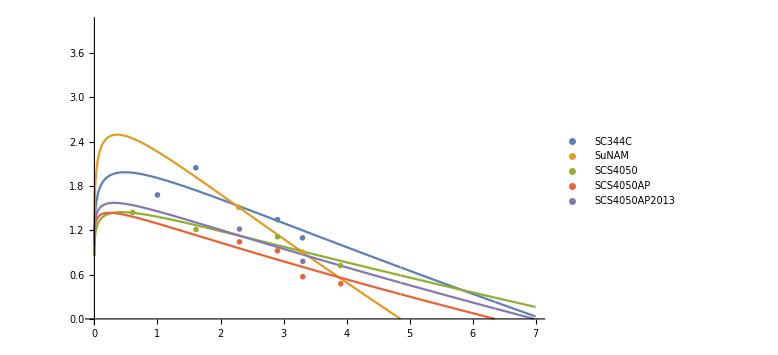

```mathematica
(*Plotting all the results*)
(*SC344C={{1.,1.68},{1.6081819581280792,2.0476190476190474},{2.9050141967706624,1.345238095238095},{3.3008560823754785,1.0982142857142854}};
SuNAM={{2.2905505952380953,1.5119047619047619},{3.300300184729064,0.9047619047619044}};
SCS4050={{0.6064458470169677,1.443452380952381},{1.6115258962780517,1.2113095238095235},{2.9043471195949646,1.113095238095238},{3.903226772030651,0.7232142857142854}};
SCS4050AP={{2.3007021414887796,1.044642857142857},{2.9037997742200328,0.9226190476190472},{3.305089456759716,0.571428571428571},{3.908264059934319,0.47619047619047583}};
SCS4050AP2013={{2.3011981732348112,1.2172619047619047},{3.305688115763547,0.7797619047619047}};*)
n1= 0.33318;
fL0=7;
Show[Plot[{f[phif[fL/fL0,d344C,n1],c344C],f[phif[fL/fL0,dSuNAM,n1],cSuNAM],f[phif[fL/fL0,dSCS4050,n1],cSCS4050],f[phif[fL/fL0,dSCS4050,n1]+ϵSCS4050AP,cSCS4050]/f[ϵSCS4050AP,cSCS4050],f[phif[fL/fL0,dSCS4050,n1]+ϵSCS4050AP2013,cSCS4050]/f[ϵSCS4050AP2013,cSCS4050]},{fL,0,7},PlotRange->{0,4},ImageSize->Large,PlotStyle->{Automatic,Thick}],ListPlot[{SC344C,SuNAM,SCS4050,SCS4050AP,SCS4050AP2013},PlotLegends->{"SC344C","SuNAM","SCS4050","SCS4050AP","SCS4050AP2013"},PlotMarkers->"OpenMarkers"]]
```

```mathematica
Show[Plot[y[ϕ],{ϕ,0.001,0.999},PlotStyle->{Thick,Blue},Axes->False,PlotRange->{{-.21,1.3},All},AspectRatio->1,ImageSize->500],(*Add coordinate axes as arrows*)Graphics[{Arrowheads[0.08],Thick,Arrow[{{-0.02,0},{1.23,0}}],(*x-axis*)Arrow[{{0,-0.02},{0,1.05}}]  (*y-axis*)}],(*Add tick marks*)Graphics[{Thick,Line[{{1,-0.015},{1,0.015}}],(*x tick at ϕ=1*)Line[{{-0.015,0.85},{0.015,0.85}}] (*y tick at I_c/I_c0=1*)}],(*Add text labels*)Graphics[{Text[Style["0",24,FontFamily->"Times"],{-0.04,-0.03}],Text[Style["1",24,FontFamily->"Times"],{1.01,-0.05}],Text[Style["1",24,FontFamily->"Times"],{-0.03,0.85}],Text[Style[TraditionalForm[ϕ],30,Bold,FontFamily->"Times"],{1.25,-0.01}],Text[Style[Subscript[Ic,c]/Superscript[Subscript[Ic,c],0],30,Bold,FontFamily->"Times"],{-0.12,1.0}]}]]
```

```mathematica
(*Fitting data to H and T.*)
```

```mathematica
(*Experimental Data for volume fraction--Method 3*)
```

```mathematica
(*-Graphics-
We will be extracting data from the following figures.*)
```

{{7.01299,131.146},{8,115.},{9.01299,100.938},{10.026,90.5208},{11.013,81.1458},{12.,73.3333},{12.987,66.0417},{14.,59.7917},{14.987,54.5833}}

{{7.01299,0},{8,0},{9.01299,0},{10.,97.8125},{11.013,87.9167},{12.,78.0208},{12.987,69.6875},{14.,61.875},{15.013,54.5833}}

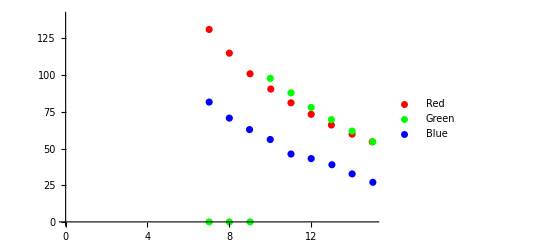

{{7.01299,0.622716},{8,0.615036},{8.98701,0.623323},{10.,0.620253},{11.013,0.569961},{12.,0.588068},{13.013,0.589905},{14.,0.547038},{15.013,0.494275}}

{{10.,1.08055},{11.013,1.08344},{12.,1.06392},{12.987,1.05521},{14.,1.03484},{15.013,1.}}

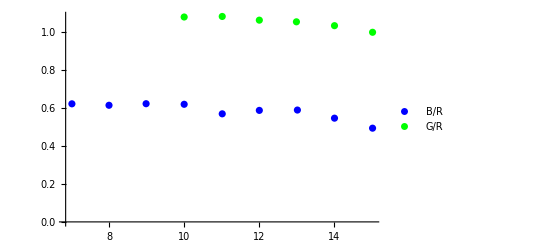

```mathematica
(*Data for Ic for SCS4050AP 2013 at 40K. H perp to the surface of the sample.*)
SCS4050AP201340KRed={{7.012987012987011,131.14583333333337},{8,115.00000000000003},{9.012987012987015,100.9375},{10.025974025974026,90.52083333333337},{11.012987012987015,81.14583333333337},{12.000000000000004,73.33333333333337},{12.987012987012985,66.04166666666669},{14.000000000000004,59.791666666666686},{14.987012987012992,54.583333333333314}}
SCS4050AP201340KGreen={{7.012987012987011,0},{8,0},{9.012987012987015,0},{10.000000000000004,97.8125},{11.012987012987015,87.91666666666669},{12.000000000000004,78.02083333333337},{12.987012987012985,69.6875},{14.000000000000004,61.875},{15.012987012987015,54.583333333333314}}
SCS4050AP201340KBlue=Drop[{{4.0000000000000036,123.333333333333344},{4.987012987012985,108.75000000000003},{6,91.04166666666669},{7.012987012987011,81.66666666666669},{8,70.72916666666669},{8.987012987012989,62.916666666666686},{10.000000000000004,56.14583333333337},{11.012987012987015,46.25},{12.000000000000004,43.125},{13.012987012987015,38.958333333333314},{14.000000000000004,32.708333333333314},{15.012987012987015,26.97916666666663}},3];
ListPlot[{SCS4050AP201340KRed,SCS4050AP201340KGreen,SCS4050AP201340KBlue},PlotStyle->{Red,Green,Blue},PlotLegends->{"Red","Green","Blue"},PlotRange->{{0,15},{0,140}}]
Length[SCS4050AP201340KRed];
Length[SCS4050AP201340KBlue];
Length[SCS4050AP201340KGreen];
IcBbRSCS40K=Transpose[{SCS4050AP201340KBlue[[All,1]],SCS4050AP201340KBlue[[All,2]]/SCS4050AP201340KRed[[All,2]]}]
IcGbRSCS40K=Drop[Transpose[{SCS4050AP201340KGreen[[All,1]],SCS4050AP201340KGreen[[All,2]]/SCS4050AP201340KRed[[All,2]]}],3]
ListPlot[{IcBbRSCS40K,IcGbRSCS40K},PlotLegends->{"B/R","G/R"},PlotStyle->{Blue,Green}]
```

{{5.01299,119.74},{6.,98.4416},{7.01299,83.8961},{8.,71.4286},{8.98701,62.0779},{10.,52.7273},{10.987,45.974},{12.,40.2597},{12.987,35.0649},{14,30.9091},{15.013,27.7922}}

{{4.97788,53.0806},{5.97345,43.128},{7.00221,35.8294},{7.99779,29.1943},{8.99336,23.8863},{9.98894,19.9052},{10.9845,17.2512},{11.9801,13.9336},{12.9757,11.9431},{14.0044,9.95261},{15.,7.96209}}

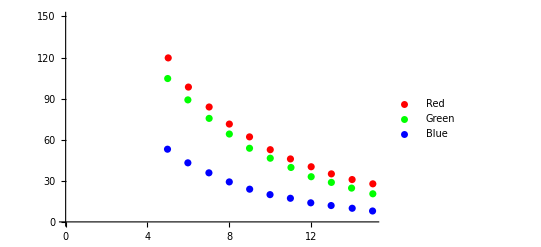

11

11

11

{{4.97788,0.443298},{5.97345,0.438107},{7.00221,0.427069},{7.99779,0.40872},{8.99336,0.384779},{9.98894,0.377513},{10.9845,0.375238},{11.9801,0.346094},{12.9757,0.3406},{14.0044,0.321996},{15.,0.286486}}

{{4.98701,0.874187},{5.97403,0.905013},{7.01299,0.900929},{8.,0.898182},{8.98701,0.866109},{10.,0.881773},{11.013,0.864407},{12.,0.819355},{12.987,0.822222},{13.974,0.798319},{15.013,0.738318}}

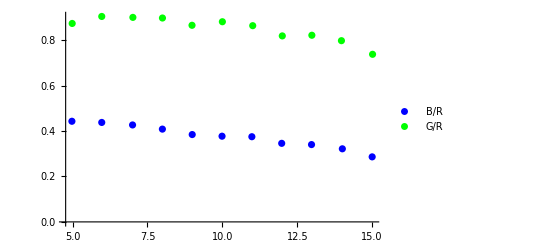

```mathematica
(*Data for Ic for SCS4050AP 2013 at 50K. H perp to the surface of the sample.*)
SCS4050AP201350KRed={{3.999999999999993,147.27272727272725},{5.012987012987011,119.74025974025972},{5.999999999999993,98.44155844155853},{7.012987012987008,83.89610389610402},{7.9999999999999964,71.42857142857156},{8.987012987012982,62.07792207792227},{9.999999999999996,52.72727272727286},{10.987012987012985,45.97402597402606},{11.999999999999996,40.2597402597404},{12.987012987012982,35.064935064935185},{14,30.909090909091105},{15.012987012987004,27.792207792207932}};
SCS4050AP201350KGreen={{4.987012987012982,104.67532467532476},{5.97402597402597,89.09090909090924},{7.012987012987008,75.58441558441575},{7.9999999999999964,64.1558441558443},{8.987012987012982,53.76623376623388},{9.999999999999996,46.49350649350663},{11.012987012987008,39.74025974025983},{11.999999999999996,32.98701298701303},{12.987012987012982,28.831168831168952},{13.97402597402597,24.67532467532476},{15.012987012987004,20.519480519480567}};
SCS4050AP201350KBlue={{0.9955752212389406,118.10426540284323},{1.991150442477874,96.87203791469176},{2.986725663716804,78.95734597156377},{3.9823008849557553,65.02369668246456},{4.977876106194692,53.080568720379006},{5.973451327433626,43.12796208530801},{7.0022123893805315,35.829383886255755},{7.997787610619472,29.194312796208692},{8.99336283185841,23.886255924170655},{9.988938053097343,19.905213270142212},{10.984513274336276,17.25118483412325},{11.98008849557522,13.933649289099662},{12.975663716814157,11.943127962085555},{14.00442477876106,9.95260663507122},{14.999999999999996,7.962085308057112}};
SCS4050AP201350KRed=Drop[SCS4050AP201350KRed,1]
SCS4050AP201350KBlue=Drop[SCS4050AP201350KBlue,4]
ListPlot[{SCS4050AP201350KRed,SCS4050AP201350KGreen,SCS4050AP201350KBlue},PlotStyle->{Red,Green,Blue},PlotLegends->{"Red","Green","Blue"},PlotRange->{{0,15},{0,150}}]
Length[SCS4050AP201350KRed]
Length[SCS4050AP201350KBlue]
Length[SCS4050AP201350KGreen]
IcBbRSCS50K=Transpose[{SCS4050AP201350KBlue[[All,1]],SCS4050AP201350KBlue[[All,2]]/SCS4050AP201350KRed[[All,2]]}]
IcGbRSCS50K=Transpose[{SCS4050AP201350KGreen[[All,1]],SCS4050AP201350KGreen[[All,2]]/SCS4050AP201350KRed[[All,2]]}]
ListPlot[{IcBbRSCS50K,IcGbRSCS50K},PlotLegends->{"B/R","G/R"},PlotStyle->{Blue,Green}]
```

```mathematica
(*Creating data collecting temperature.*)
IcBbRSCS40K;
IcBbRSCS50K;
IcBbRSCS={IcBbRSCS40K,IcBbRSCS50K};
IcGbRSCS40K;
IcGbRSCS50K;
IcGbRSCS={IcGbRSCS40K,IcGbRSCS50K};
Dimensions[IcGbRSCS[[1]]][[1]];
IcGbRSCS[[1,2,2]]
```

1.08344

```mathematica
Clear[ϵ0,ϵ1,ϵ2,ϵ3,ϵ4,c0,c1,c2,c3,c4,c5,c6,c7,d0,d1,d2,d3,d4,d5,d6,d7,n0,n1,n2,n3,n4,n5,n6,n7,H0,fL0]
ϵ0=0.03809094863656232;
c0=7.739;
n0=0.33381;
d0=0.993567;
fL0=7;
word={"I_c/((I^0)_c) at 40 K at H=","I_c/((I^0)_c) at 50K at H="};
H0={9,4};
Manipulate[{Soln1=NMinimize[{(f[phif[2.3/fL0,d,n0]+ϵ0,c1]/f[ϵ0,c1]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d,n0]+ϵ0,c1]/f[ϵ0,c1]-IcBbRSCS[[T,H,2]])^2,c1>0.001},{c1}];Soln2=NMinimize[{(f[phif[2.3/fL0,d2,n0]+ϵ0,c]/f[ϵ0,c]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d2,n0]+ϵ0,c]/f[ϵ0,c]-IcBbRSCS[[T,H,2]])^2,d2>0.001},{d2}];Soln3=NMinimize[{(f[phif[2.3/fL0,d3,n0]+ϵ0,c3]/f[ϵ0,c3]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d3,n0]+ϵ0,c3]/f[ϵ0,c3]-IcBbRSCS[[T,H,2]])^2,c3>1.5,d3>0.001},{c3,d3}];
Show[Plot[{f[phif[fL/fL0,d,n]+ϵ0,c]/f[ϵ0,c],f[phif[fL/fL0,d,n]+ϵ0,c1/.Soln1[[2]]]/f[ϵ0,c1/.Soln1[[2]]],f[phif[fL/fL0,d2/.Soln2[[2]],n]+ϵ0,c]/f[ϵ0,c],f[phif[fL/fL0,d3/.Soln3[[2]],n]+ϵ0,c3/.Soln3[[2]]]/f[ϵ0,c3/.Soln3[[2]]]},{fL,0,7},PlotRange->{0,4},ImageSize->Large,PlotStyle->{Blue,Yellow,Green,Red},PlotLegends->{"Original",Row[{"c1=",c1/.Soln1[[2]]}],Row[{"d2=",d2/.Soln2[[2]]}],Row[{"c3=",c3/.Soln3[[2]],", d3=",d3/.Soln3[[2]]}]}],ListPlot[{{2.3,IcGbRSCS[[T,H,2]]},{3.3,IcBbRSCS[[T,H,2]]}},PlotLegends->{Row[word[[T]],H+H0[[T]]]}]],{{2.3,IcGbRSCS[[T,H,2]]},{3.3,IcBbRSCS[[T,H,2]]}}},{{c,c0},0,20},{{d,d0},0,10},{{fL0,fL01},0,20},{T,1,2,1},{H,1,Min[Dimensions[IcBbRSCS[[T]]][[1]],Dimensions[IcGbRSCS[[T]]][[1]]],1}]
```

```mathematica
Clear[ϵ0,ϵ1,ϵ2,ϵ3,ϵ4,c0,c1,c2,c3,c4,c5,c6,c7,d0,d1,d2,d3,d4,d5,d6,d7,n0,n1,n2,n3,n4,n5,n6,n7,H0,fL0]
ϵ0=0.03809094863656232;
c0=7.739;
n0=0.33381;
d0=0.993567;
fL0=7;
word={"I_c/((I^0)_c) at 40 K at H=","I_c/((I^0)_c) at 50K at H="};
H0={9,4}
Manipulate[{Soln1=NMinimize[{(f[phif[2.3/fL0,d,n0]+ϵ0,c1]/f[ϵ0,c1]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d,n0]+ϵ0,c1]/f[ϵ0,c1]-IcBbRSCS[[T,H,2]])^2,c1>0.001&& c1<20},{c1}];Soln2=NMinimize[{(f[phif[2.3/fL0,d2,n0]+ϵ0,c]/f[ϵ0,c]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d2,n0]+ϵ0,c]/f[ϵ0,c]-IcBbRSCS[[T,H,2]])^2,d2>0.001},{d2}];Soln3=NMinimize[{(f[phif[2.3/fL0,d3,n0]+ϵ0,c3]/f[ϵ0,c3]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d3,n0]+ϵ0,c3]/f[ϵ0,c3]-IcBbRSCS[[T,H,2]])^2,c3>0.1,d3>0.001},{c3,d3}];
Show[Plot[{f[phif[fL/fL0,d,n]+ϵ0,c]/f[ϵ0,c],f[phif[fL/fL0,d,n]+ϵ0,c1/.Soln1[[2]]]/f[ϵ0,c1/.Soln1[[2]]],f[phif[fL/fL0,d2/.Soln2[[2]],n]+ϵ0,c]/f[ϵ0,c],f[phif[fL/fL0,d3/.Soln3[[2]],n]+ϵ0,c3/.Soln3[[2]]]/f[ϵ0,c3/.Soln3[[2]]]},{fL,0,7},PlotRange->{0,4},ImageSize->Large,PlotStyle->{Blue,Yellow,Green,Red,Black},PlotLegends->{"Original",Row[{"c1=",c1/.Soln1[[2]]}],Row[{"d2=",d2/.Soln2[[2]]}],Row[{"c3=",c3/.Soln3[[2]],", d3=",d3/.Soln3[[2]]}]}],ListPlot[{{2.3,IcGbRSCS[[T,H,2]]},{3.3,IcBbRSCS[[T,H,2]]}},PlotLegends->{Row[word[[T]],H+H0[[T]]]}]],{{2.3,IcGbRSCS[[T,H,2]]},{3.3,IcBbRSCS[[T,H,2]]}}},{{c,c0},0,20},{{n,n0},0,2},{{d,d0},0,10},{{fL0,fL01},0,20},{T,1,2,1},{H,1,Min[Dimensions[IcBbRSCS[[T]]][[1]],Dimensions[IcGbRSCS[[T]]][[1]]],1}]
```

{9,4}

```mathematica
T=1;
H=1;
IcGbRSCS[[T,H,2]]
IcBbRSCS[[T,H,2]]
Soln11=NMinimize[{(f[phif[2.3/fL0,d0,n0]+ϵ1,c0]/f[ϵ1,c0]-1.0805523590333712)^2+(f[phif[3.3/fL0,d0,n0]+ϵ1,c0]/f[ϵ1,c0]-0.6227164416203336)^2,ϵ1>0},ϵ1]
ϵ1/.Soln11[[2]]
```

1.08055

0.622716

{0.0168867,{ϵ1→0.068225}}

0.068225

```mathematica
Clear[ϵ0,ϵ1,ϵ2,ϵ3,ϵ4,c0,c1,c2,c3,c4,c5,c6,c7,d0,d1,d2,d3,d4,d5,d6,d7,n0,n1,n2,n3,n4,n5,n6,n7,H0,fL0]
ϵ0=0.0432;
c0=7.739;
n0=0.388097;
d0=0.993567;
fL0=7;
word={"I_c/((I^0)_c) at 40 K at H=","I_c/((I^0)_c) at 50K at H="};
H0={9,4}
Manipulate[{Soln3=NMinimize[{(f[phif[2.3/fL0,d3,n4]+ϵ0,c3]/f[ϵ0,c3]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d3,n4]+ϵ0,c3]/f[ϵ0,c3]-IcBbRSCS[[T,H,2]])^2,c3>1.5,d3>0.001, n4>0.001},{c3,d3, n4}];

Show[Plot[{f[phif[fL/fL0,d,n]+ϵ0,c]/f[ϵ0,c],f[phif[fL/fL0,d3/.Soln3[[2]],n4/.Soln4[[2]]]+ϵ0,c3/.Soln3[[2]]]/f[ϵ0,c3/.Soln3[[2]]]},{fL,0,7},PlotRange->{0,5},ImageSize->Large,PlotStyle->{Blue,Yellow,Green,Red,Black},PlotLegends->{"Original",Row[{"c3=",c3/.Soln3[[2]],", d3=",d3/.Soln3[[2]], ", n4=", n4/.Soln3[[2]]}]}],ListPlot[{{2.3,IcGbRSCS[[T,H,2]]},{3.3,IcBbRSCS[[T,H,2]]}},PlotLegends->{Row[word[[T]],H+H0[[T]]]}]],{{2.3,IcGbRSCS[[T,H,2]]},{3.3,IcBbRSCS[[T,H,2]]}}},{{c,c0},0,20},{{n,n0},0,2},{{d,d0},0,10},{{fL0,fL01},0,20},{T,1,2,1},{H,1,Min[Dimensions[IcBbRSCS[[T]]][[1]],Dimensions[IcGbRSCS[[T]]][[1]]],1}]
```

{9,4}

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification IcBbRSCS⟦1,1,2⟧ is longer than depth of object.

NMinimize::nnum: The function value (((1+3.16718 (0.733867+ϵ0)) Log[ϵ0] (0.266133-ϵ0+Log[0.733867+ϵ0]))/((1+3.16718 ϵ0) (1-ϵ0+Log[ϵ0]) Log[0.733867+ϵ0])-IcBbRSCS⟦1,1,2⟧)^2+(((1+3.16718 (0.496791+ϵ0)) Log[ϵ0] (0.503209-ϵ0+Log[0.496791+ϵ0]))/((1+3.16718 ϵ0) (1-ϵ0+Log[ϵ0]) Log[0.496791+ϵ0])-IcGbRSCS⟦1,1,2⟧)^2 is not a number at {c3,d3,n4} = {3.16718,1.65412,1.08073}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

ReplaceAll::reps: {c3,d3,n4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification IcBbRSCS⟦1,1,2⟧ is longer than depth of object.

NMinimize::nnum: The function value (((1+3.16718 (0.733867+ϵ0)) Log[ϵ0] (0.266133-ϵ0+Log[0.733867+ϵ0]))/((1+3.16718 ϵ0) (1-ϵ0+Log[ϵ0]) Log[0.733867+ϵ0])-IcBbRSCS⟦1,1,2⟧)^2+(((1+3.16718 (0.496791+ϵ0)) Log[ϵ0] (0.503209-ϵ0+Log[0.496791+ϵ0]))/((1+3.16718 ϵ0) (1-ϵ0+Log[ϵ0]) Log[0.496791+ϵ0])-IcGbRSCS⟦1,1,2⟧)^2 is not a number at {c3,d3,n4} = {3.16718,1.65412,1.08073}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

ReplaceAll::reps: {c3,d3,n4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification IcBbRSCS⟦1,1,2⟧ is longer than depth of object.

NMinimize::nnum: The function value (((1+3.16718 (0.733867+ϵ0)) Log[ϵ0] (0.266133-ϵ0+Log[0.733867+ϵ0]))/((1+3.16718 ϵ0) (1-ϵ0+Log[ϵ0]) Log[0.733867+ϵ0])-IcBbRSCS⟦1,1,2⟧)^2+(((1+3.16718 (0.496791+ϵ0)) Log[ϵ0] (0.503209-ϵ0+Log[0.496791+ϵ0]))/((1+3.16718 ϵ0) (1-ϵ0+Log[ϵ0]) Log[0.496791+ϵ0])-IcGbRSCS⟦1,1,2⟧)^2 is not a number at {c3,d3,n4} = {3.16718,1.65412,1.08073}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

ReplaceAll::reps: {c3,d3,n4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Clear[ϵ0,ϵ1,ϵ2,ϵ3,ϵ4,c0,c1,c2,c3,c4,c5,c6,c7,d0,d1,d2,d3,d4,d5,d6,d7,n0,n1,n2,n3,n4,n5,n6,n7,H0,fL0]
ϵ0=0.0432;
c0=7.739;
n0=0.388097;
d0=0.993567;
fL0=7;
word={"I_c/((I^0)_c) at 40 K at H=","I_c/((I^0)_c) at 50K at H="};
H0={9,4}
Manipulate[{Soln1=NMinimize[{(f[phif[2.3/fL0,d,n0]+ϵ0,c1]/f[ϵ0,c1]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d,n0]+ϵ0,c1]/f[ϵ0,c1]-IcBbRSCS[[T,H,2]])^2,c1>0.001},{c1}];Soln2=NMinimize[{(f[phif[2.3/fL0,d2,n0]+ϵ0,c]/f[ϵ0,c]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d2,n0]+ϵ0,c]/f[ϵ0,c]-IcBbRSCS[[T,H,2]])^2,d2>0.001},{d2}];Soln3=NMinimize[{(f[phif[2.3/fL0,d3,n0]+ϵ0,c3]/f[ϵ0,c3]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d3,n0]+ϵ0,c3]/f[ϵ0,c3]-IcBbRSCS[[T,H,2]])^2,c3>0.001,d3>0.001},{c3,d3}];
Soln4=NMinimize[{(f[phif[2.3/fL0,d,n4]+ϵ0,c]/f[ϵ0,c]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d,n4]+ϵ0,c]/f[ϵ0,c]-IcBbRSCS[[T,H,2]])^2,n4>0.001},{n4}];
Soln5=NMinimize[{(f[phif[2.3/fL0,d5,n5]+ϵ0,c5]/f[ϵ0,c5]-IcGbRSCS[[T,H,2]])^2+(f[phif[3.3/fL0,d5,n5]+ϵ0,c5]/f[ϵ0,c5]-IcBbRSCS[[T,H,2]])^2,c5>0.001,d5>0.001,n5>0.001},{c5, d5, n5}];
Show[Plot[{f[phif[fL/fL0,d,n]+ϵ0,c]/f[ϵ0,c],f[phif[fL/fL0,d,n]+ϵ0,c1/.Soln1[[2]]]/f[ϵ0,c1/.Soln1[[2]]],f[phif[fL/fL0,d2/.Soln2[[2]],n]+ϵ0,c]/f[ϵ0,c],f[phif[fL/fL0,d3/.Soln3[[2]],n]+ϵ0,c3/.Soln3[[2]]]/f[ϵ0,c3/.Soln3[[2]]],f[phif[fL/fL0,d0,n4/.Soln4[[2]]]+ϵ0,c0]/f[ϵ0,c0], f[phif[fL/fL0,d5/.Soln5[[2]],n5/.Soln5[[2]]]+ϵ0,c5/.Soln5[[2]]]/f[ϵ0,c5/.Soln5[[2]]]},{fL,0,7},PlotRange->{0,5},ImageSize->Large,PlotStyle->{Blue,Yellow,Green,Red,Black, Orange},PlotLegends->{"Original",Row[{"c1=",c1/.Soln1[[2]]}],Row[{"d2=",d2/.Soln2[[2]]}],Row[{"c3=",c3/.Soln3[[2]],", d3=",d3/.Soln3[[2]]}],Row[{"n4=",n4/.Soln4[[2]]}],Row[{"c5=",c5/.Soln5[[2]],", d5=",d5/.Soln5[[2]],", n5=",n5/.Soln5[[2]]}]}],ListPlot[{{2.3,IcGbRSCS[[T,H,2]]},{3.3,IcBbRSCS[[T,H,2]]}},PlotLegends->{Row[word[[T]],H+H0[[T]]]}]],{{2.3,IcGbRSCS[[T,H,2]]},{3.3,IcBbRSCS[[T,H,2]]}}},{{c,c0},0,20},{{n,n0},0,2},{{d,d0},0,10},{{fL0,fL01},0,20},{T,1,2,1},{H,1,Min[Dimensions[IcBbRSCS[[T]]][[1]],Dimensions[IcGbRSCS[[T]]][[1]]],1}]
```

{9,4}

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification IcBbRSCS⟦1,1,2⟧ is longer than depth of object.

NMinimize::nnum: The function value (((1+0.0924636 (Times[«2»]+ϵ0)) Log[ϵ0] (1-0.993567 0.471429^n0-ϵ0+Log[Times[«2»]+ϵ0]))/((1+0.0924636 ϵ0) (1-ϵ0+Log[ϵ0]) Log[Times[«2»]+ϵ0])-IcBbRSCS⟦1,1,2⟧)^2+(((1+0.0924636 (Times[«2»]+ϵ0)) Log[ϵ0] (1-0.993567 0.328571^n0-ϵ0+Log[Times[«2»]+ϵ0]))/((1+0.0924636 ϵ0) (1-ϵ0+Log[ϵ0]) Log[Times[«2»]+ϵ0])-IcGbRSCS⟦1,1,2⟧)^2 is not a number at {c1} = {0.0924636}.

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::ivar: 0.993567 is not a valid variable.

NMinimize::nnum: The function value (((1+1.91962 (Times[«2»]+ϵ0)) Log[ϵ0] (1-1.66451 0.471429^n0-ϵ0+Log[Times[«2»]+ϵ0]))/((1+1.91962 ϵ0) (1-ϵ0+Log[ϵ0]) Log[Times[«2»]+ϵ0])-IcBbRSCS⟦1,1,2⟧)^2+(((1+1.91962 (Times[«2»]+ϵ0)) Log[ϵ0] (1-1.66451 0.328571^n0-ϵ0+Log[Times[«2»]+ϵ0]))/((1+1.91962 ϵ0) (1-ϵ0+Log[ϵ0]) Log[Times[«2»]+ϵ0])-IcGbRSCS⟦1,1,2⟧)^2 is not a number at {c3,d3} = {1.91962,1.66451}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

ReplaceAll::reps: {c1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.993567} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {c3,d3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMinimize::ivar: 0.993567 is not a valid variable.

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification IcBbRSCS⟦1,1,2⟧ is longer than depth of object.

NMinimize::nnum: The function value (((1+0.0924636 (Times[«2»]+ϵ0)) Log[ϵ0] (1-0.993567 0.471429^n0-ϵ0+Log[Times[«2»]+ϵ0]))/((1+0.0924636 ϵ0) (1-ϵ0+Log[ϵ0]) Log[Times[«2»]+ϵ0])-IcBbRSCS⟦1,1,2⟧)^2+(((1+0.0924636 (Times[«2»]+ϵ0)) Log[ϵ0] (1-0.993567 0.328571^n0-ϵ0+Log[Times[«2»]+ϵ0]))/((1+0.0924636 ϵ0) (1-ϵ0+Log[ϵ0]) Log[Times[«2»]+ϵ0])-IcGbRSCS⟦1,1,2⟧)^2 is not a number at {c1} = {0.0924636}.

Part::partd: Part specification IcGbRSCS⟦1,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

NMinimize::ivar: 1.12959 is not a valid variable.

NMinimize::nnum: The function value (((1+1.91962 (Times[«2»]+ϵ0)) Log[ϵ0] (1-1.66451 0.471429^n0-ϵ0+Log[Times[«2»]+ϵ0]))/((1+1.91962 ϵ0) (1-ϵ0+Log[ϵ0]) Log[Times[«2»]+ϵ0])-IcBbRSCS⟦1,1,2⟧)^2+(((1+1.91962 (Times[«2»]+ϵ0)) Log[ϵ0] (1-1.66451 0.328571^n0-ϵ0+Log[Times[«2»]+ϵ0]))/((1+1.91962 ϵ0) (1-ϵ0+Log[ϵ0]) Log[Times[«2»]+ϵ0])-IcGbRSCS⟦1,1,2⟧)^2 is not a number at {c3,d3} = {1.91962,1.66451}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

ReplaceAll::reps: {c1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1.12959} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {c3,d3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMinimize::ivar: 1.12959 is not a valid variable.